```mathematica
predictions=Import["C:\\Users\\Renay\\Downloads\\predictions (1).csv"][[2;;All,1]];
```

```mathematica
ts=TimeSeries[predictions]
```

TimeSeries[…]

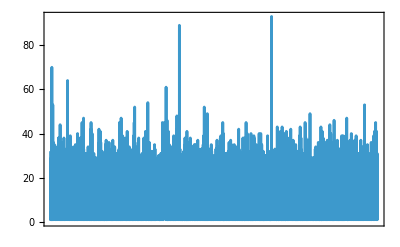

```mathematica
DateListPlot[ts,{2015,1,1},PlotRange->All]
```

```mathematica
tsm=TimeSeriesModelFit[ts]
```

TimeSeriesModel[…]

```mathematica
Normal[tsm]
```

MAProcess[11.5993,{},68.9079]

```mathematica
CovarianceFunction[MAProcess[11.599305800682433,{},68.907863972729],{0,100}]
```

TimeSeries[…]

```mathematica
WeakStationarity[MAProcess[11.599305800682433,{},68.907863972729]]
```

True

```mathematica
tsm["ParameterTable"]
```

Missing[NotAvailable]

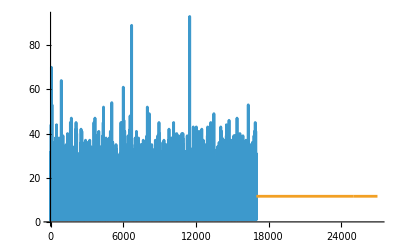

```mathematica
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{10000}]},PlotRange->All]
```